```mathematica
Integrate[Sin[x]Exp[- x],{x,0,∞}]
```

1/2

```mathematica
Integrate[Sin[x]Exp[- x],{x,0,1}]
%*1.
```

-(-ⅇ+Cos[1]+Sin[1])/(2 ⅇ)

0.245837

```mathematica
D[c1/(λ^5(Exp[c2/(λ T)]-1)),T]
%//Simplify
%//FortranForm
%//FullSimplify
```

(5.38357×10^-18 ⅇ^(0.0143878/(T λ)))/((-1+ⅇ^(0.0143878/(T λ)))^2 T^2 λ^6)

(5.38357×10^-18 ⅇ^(0.0143878/(T λ)))/((-1.+ⅇ^(0.0143878/(T λ)))^2 T^2 λ^6)

(5.38357×10^-18 ⅇ^(0.0143878/(T λ)))/((-1.+ⅇ^(0.0143878/(T λ)))^2 T^2 λ^6)

(5.383567671403015e-18*E**(0.014387752249999998/(T*λ)))/
     -  ((-1. + E**(0.014387752249999998/(T*λ)))**2*T**2*λ**6)

```mathematica
h=6.62607004*10^-34
c0=299792458
2*π*h*c0^2
k=1.38064852*10^-23
h c0/k
c1=3.74177118*10^-16;
c2=14387.75225*10^-6;
eb[λ_,T_]=c1/(λ^5(Exp[c2/(λ T)]-1));
ebdt[λ_,T_]=D[c1/(λ^5(Exp[c2/(λ T)]-1)),T];
eb[0.507 10^-6,1000]/π*10^-6
ebdt[0.507 10^-6,1000]/π*10^-6
σb=(π^4 c1)/(15 c2^4)
TT=1000;
σb TT^4/π
```

6.62607×10^-34

299792458

3.74177×10^-16

1.38065×10^-23

0.0143878

0.00168418

0.0000477939

5.6704×10^-8

18049.4

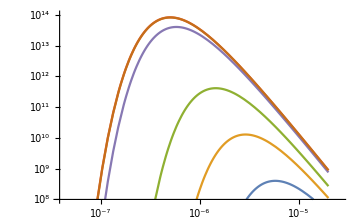

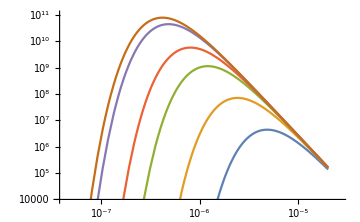

```mathematica
LogLogPlot[{eb[λ,500],eb[λ,1000],eb[λ,2000],eb[λ,5777],eb[λ,5000],eb[λ,5762]},{λ,0.5*10^-7,20*10^-6},PlotRange->{10^8,10^14}]

LogLogPlot[{ebdt[λ,500],ebdt[λ,1000],ebdt[λ,2000],ebdt[λ,3000],ebdt[λ,5000],ebdt[λ,5762]},{λ,0.5*10^-7,20*10^-6},PlotRange->{10^4,10^11}]
```

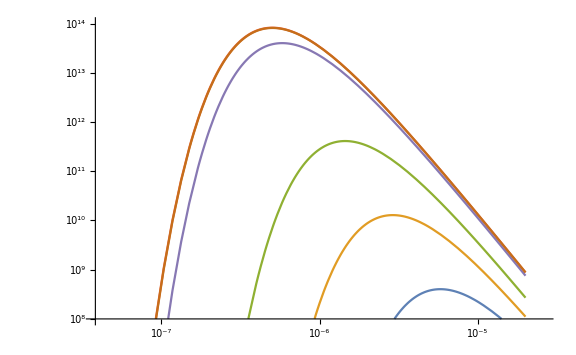

```mathematica
Show[%36,ImageSize->Large]
```

```mathematica
eb[0.0000029,1000.0]
```

1.2867×10^10

```mathematica
NIntegrate[ebdt[λ,2911],{λ,0,∞}]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in λ near {λ} = {4.64278×10^-7}. NIntegrate obtained 5595. and 0.15237 for the integral and error estimates.

5595.

```mathematica
NIntegrate[eb[λ,2911],{λ,0,∞}]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in λ near {λ} = {1.48905×10^-6}. NIntegrate obtained 4.07176×10^6 and 36.8657 for the integral and error estimates.

4.07176×10^6

```mathematica
Integrate[θ ϕ λ,{θ,0,π},{ϕ,0,2π},{λ,0.28*10^-6,4.*10^-6}]
```

7.75454×10^-10

```mathematica
Integrate[θ ϕ λ,{θ,0,π},{ϕ,0,2π},{λ,0.28,4.}]
```

775.454

```mathematica
NIntegrate[eb[λ,5777],{λ,0,∞}]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in λ near {λ} = {4.64278×10^-7}. NIntegrate obtained 6.31572×10^7 and 915.107 for the integral and error estimates.

6.31572×10^7

```mathematica
Integrate[  λ r^2 Sin[θ],{r,0,60 10^-9},{θ,0,π},{ϕ,0,2π},{λ,0.28*10^-6,4.*10^-6}]
```

7.20276×10^-33